```mathematica
dir="D:\\better output 3";
```

```mathematica
dir="D:\\betterOutput";
```

```mathematica
GetNumberOfCells[frameNo_]:=Module[{path,i,items,nOrganisms},
path = StringForm["``\\output\\frame``.json",dir,frameNo];
{i}=Import[path//ToString];
items = "Items"/.i;
nOrganisms=DeleteCases["o"/.items,-1];
Counts[Transpose[Tally[nOrganisms]]⟦2⟧]
]
```

```mathematica
GetNumberOfCells[57200]
```

<|1→2836,2→50,3→7,9→3,5→1,4→5|>

```mathematica
f0=0;
fMax=41110;
df=100;
frames=Table[f,{f,f0,fMax,df}];
nOrgsList=ParallelMap[GetNumberOfOrganisms,frames];
```

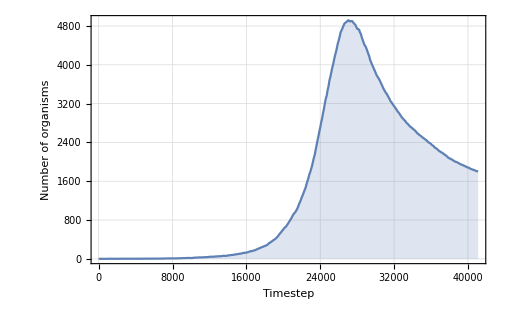

```mathematica
ListPlot[
nOrgsList,
DataRange->{f0,fMax},
Filling->Bottom,
Joined->True,
PlotRange->Full,
Frame->{{True,False},{True,False}},
FrameLabel->{"Timestep","Number of organisms"},
GridLines->Automatic
]
```